```mathematica
ClearAll["Global`*"]
```

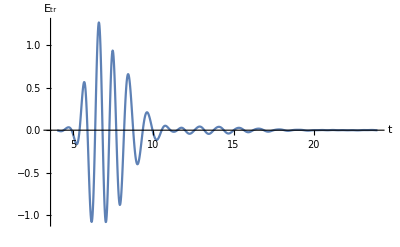

```mathematica
messyData=Import["C:\\Users\\79511\\OneDrive\\Документы\\GitHub\\Labs_Zalipaev\\lab_5\\epsdata.txt"];
lessMessyData=ToExpression@StringReplace[StringSplit[messyData],"e"->"*10^"];
data=Table[{lessMessyData[[i]],lessMessyData[[i+1]]},{i,1,Length[lessMessyData]-1,2}];
tmin=data[[1,1]];
tmax=data[[-1,1]];
ListLinePlot[data,PlotRange->All,AxesLabel->{"t","E_tr"}]
```

```mathematica
z=10^-3;(*detector position*)
c=3*10^8;
factor=N@2 Pi z/c*10^11;
k0=1;
n0=1;
τp=1;
f0=1;
fmin=0.1;
fmax=1.9;
divisionNumber=100;
d=1;
interpOrder=3;
maxIters=100;
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

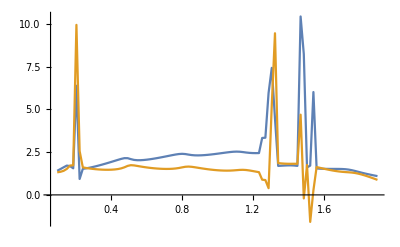

```mathematica
F[f_,τ_,f0_]:=2Sqrt[Pi] τ Exp[-2Pi (f-f0)^2 τ^2]
timeDomain=Transpose[data][[1]];
discreteExponent[f_]:=Transpose[{timeDomain,Exp[I (f t-factor)]/.{t->timeDomain}}]
multipliedFuncValues[f_]:=Transpose[data][[2]]*Transpose[discreteExponent[f]][[2]]
RealMultipliedFunction[f_]:=Transpose[{timeDomain,Re@multipliedFuncValues[f]}]
ImMultipliedFunction[f_]:=Transpose[{timeDomain,Im@multipliedFuncValues[f]}]
RealIntegral[f_]:=Integrate[Interpolation[RealMultipliedFunction[f],InterpolationOrder->interpOrder][t],{t,tmin,tmax}]
ImIntegral[f_]:=Integrate[Interpolation[ImMultipliedFunction[f],InterpolationOrder->interpOrder][t],{t,tmin,tmax}]
RealT[f_,τ_,f0_]:=(F[f,τ,f0])^-1*RealIntegral[f]
ImT[f_,τ_,f0_]:=(F[f,τ,f0])^-1*ImIntegral[f]
Φ[f_,n_,k0_,d_,τ_,f0_]:=(4n)/((n+1)^2 Exp[-I k0 n d]-(n-1)^2 Exp[I k0 n d])-(RealT[f,τ,f0]+I ImT[f,τ,f0])
fArray=N[Subdivide[fmin,fmax,divisionNumber]];
nFinder[f_,k0_,d_,τp_,f0_]:=FindRoot[Φ[f,n,k0,d,τp,f0],{n,n0}]
fnArray=ParallelTable[{fArray[[i]],nFinder[fArray[[i]],k0,d,τp,f0][[1,2]]},{i,1,Length[fArray]}];
fϵArray=Transpose[{fArray,Sqrt[fnArray[[All,2]]]}];
fϵRealArray=Transpose[{fArray,Re[fϵArray[[All,2]]]}];
fϵImArray=Transpose[{fArray,Im[fϵArray[[All,2]]]}];
ListLinePlot[{fϵRealArray,fϵImArray},PlotRange->All]
```

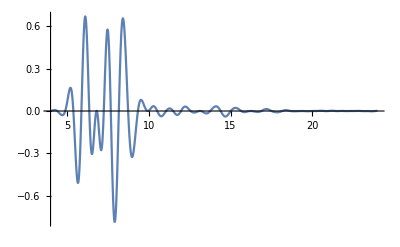

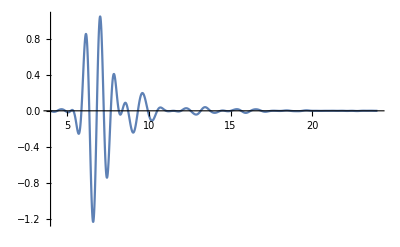

```mathematica
intfunc1=Interpolation[RealMultipliedFunction[1],InterpolationOrder->3];
intfunc2=Interpolation[ImMultipliedFunction[1],InterpolationOrder->3];
Plot[intfunc1[t],{t,tmin,tmax},PlotRange->All]
Plot[intfunc2[t],{t,tmin,tmax},PlotRange->All]
```